# RandomMaze

generate a random maze from a grid graph

## Definition

```mathematica
ClearAll[RandomMaze]
RandomMaze[{m_,n_},options:OptionsPattern[Graph]]:=Block[{g},g=GridGraph[{m,n}];Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],With[{v=First@stack},With[{adj=Cases[EdgeList[g,v<->_]/. {v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},If[adj=={},stack=Rest@stack,With[{w=RandomChoice[adj]},PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First,VertexCoordinates->GraphEmbedding[g],options]]
RandomMaze[n:{Repeated[_Integer,{2,Infinity}]},options:OptionsPattern[Graph]]:=Block[{g},g=GridGraph[n];Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],With[{v=First@stack},With[{adj=Cases[EdgeList[g,v<->_]/. {v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},If[adj=={},stack=Rest@stack,With[{w=RandomChoice[adj]},PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First,VertexCoordinates->GraphEmbedding[g],options]]
```

## Documentation

### Usage

MyFunction[{m,n}]

gives a random maze from the grid graph with m×n vertices G_(m,n).

MyFunction[{n_1,n_2,…,n_k}]

gives a random maze k-dimensional grid graph with n_1×n_2×⋯×n_k vertices G_(n_1,n_2,…,n_k).

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Make a random maze from a 10x10 grid graph:

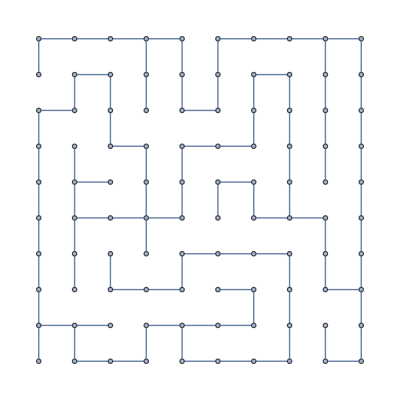

```mathematica
RandomMaze[{10,10}]
```

Make a random 10x10x10 grid for a maze:

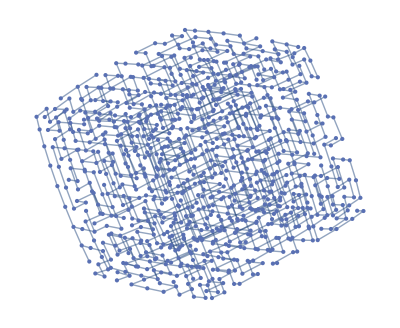

```mathematica
RandomMaze[{10,10,10}]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

Make a big maze:

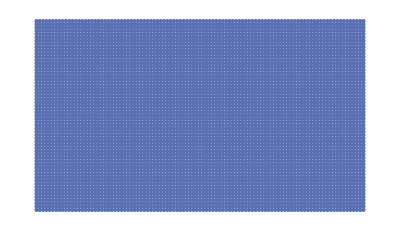

```mathematica
RandomMaze[{59,101},ImageSize->Full]
```

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

mazes

graph

breadth first search

graph traversal

shortest path algorithm

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FindShortestPath

GridGraph

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

This is based on the example in the documentation for FindShortestPath applications.